# Outliers Detection with Clustering

```mathematica
clustersNo = FindClusters[reducedOxyNo80[[11;;20,1]],Method->"MeanShift"];
```

```mathematica
Dimensions[clustersNo]
```

{2}

```mathematica
Dimensions[clustersNo[[1]]]
Dimensions[clustersNo[[2]]]
Dimensions[clustersNo[[3]]]
```

{9,80}

{1,80}

Part::partw: Part 3 of {{«1»},{{-5.41212,-5.72614,-5.86549,-5.85787,-5.73539,-5.51379,-5.18701,-4.74077,«35»,3.22611,3.76675,4.19586,4.46664,4.54487,4.42634,4.13758,«30»}}} does not exist.

{2}

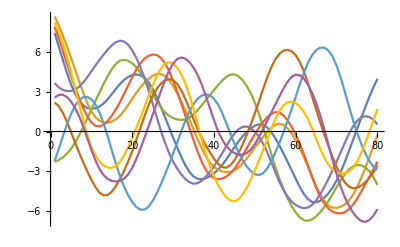
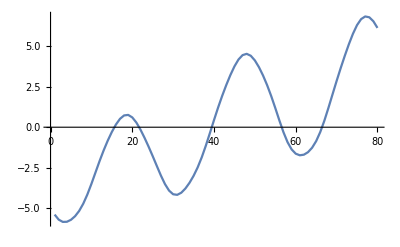
{-Graphics-→9,-Graphics-→1}

```mathematica
Table[ListLinePlot[clustersNo[[i]]]-> Length[clustersNo[[i]]],{i,Dimensions[clustersNo][[1]]}]
```

```mathematica
clusteredOxyNo = clustersNo[[1]];
```

```mathematica
clustersYes = FindClusters[reducedOxyYes80[[11;;20,1]],Method->"MeanShift"];
Dimensions[clustersYes]
```

{3}

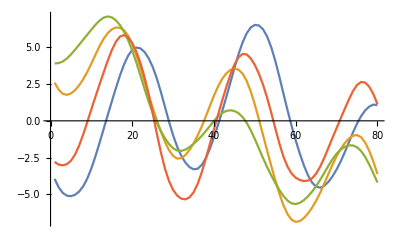
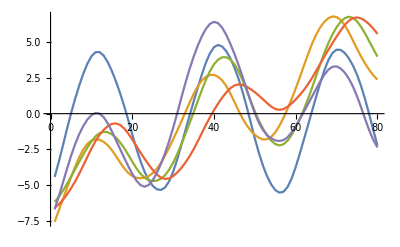
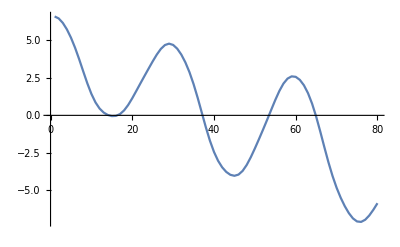
{-Graphics-→4,-Graphics-→5,-Graphics-→1}

```mathematica
Table[ListLinePlot[clustersYes[[i]]]-> Length[clustersYes[[i]]],{i,Dimensions[clustersYes][[1]]}]
```

{9,80}

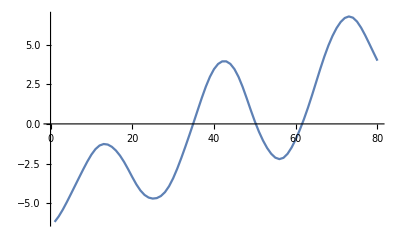

```mathematica
clusteredOxyYes = Join[clustersYes[[1]],clustersYes[[2]]];
Dimensions[clusteredOxyYes]
ListLinePlot[clusteredOxyYes[[7]]]
```

```mathematica
clustData = Join[Table[clusteredOxyYes[[i]]->"Yes",{i,Length[clusteredOxyYes]}],Table[clusteredOxyNo[[i]]->"No",{i,Length[clusteredOxyNo]}]];
```

```mathematica
clustData//Dimensions
```

{18}

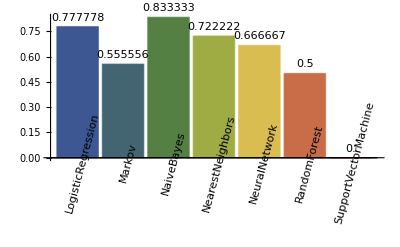

```mathematica
autoML[clustData]
```

## Archetypal on the reduced outliers set

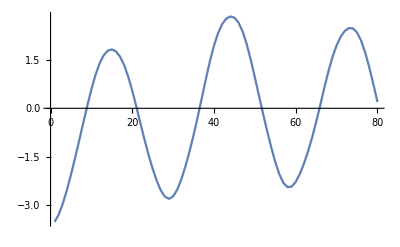

```mathematica
nooutMeanArchetypalYes = Mean[clusteredOxyYes[[All]]];
nooutMeanArchetypalNo = Mean[clusteredOxyNo[[All]]];
ListLinePlot[nooutMeanArchetypalYes]

l1DistVect[signal_List] := {ManhattanDistance[signal,nooutMeanArchetypalYes],ManhattanDistance[signal,nooutMeanArchetypalNo]}
```

```mathematica
dataDistArchDriftL1 = Join[Table[l1DistVect[clusteredOxyNo[[x]]]->"No",{x,Length[clusteredOxyNo]}],Table[l1DistVect[clusteredOxyYes[[x]]]->"Yes",{x,Length[clusteredOxyYes]}]];
```

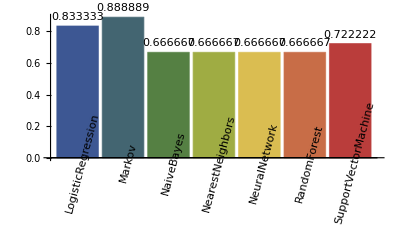

```mathematica
autoML[dataDistArchDriftL1]
```